## EdgesUsed-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 18:50:57
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

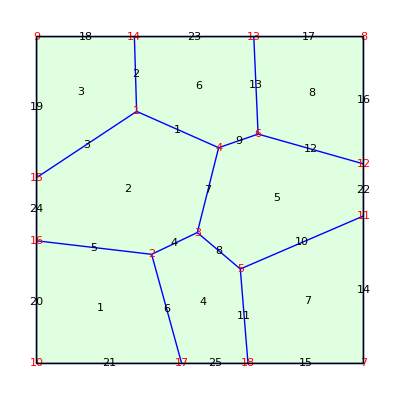

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Blue,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

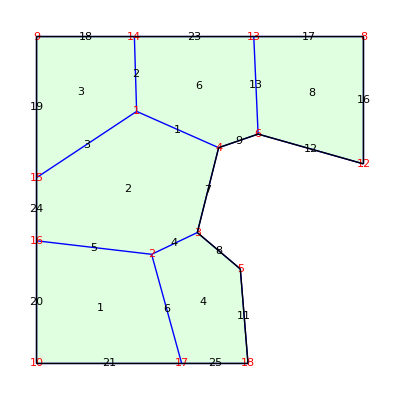

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Blue,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

Now use the “All” option to show the edges and vertices that are NOT part of any cell

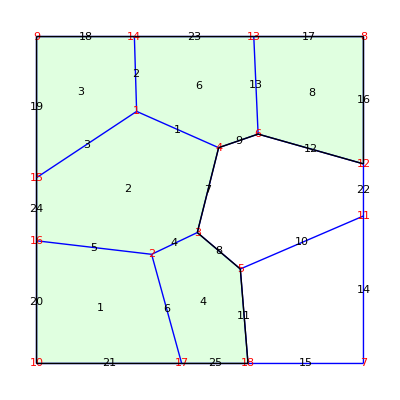

```mathematica
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Blue,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12], 
"All"-> True]
```

```mathematica
R
```

DTissue[{{-19.3866,27.102},{-14.7991,-16.6123},{-0.826609,-9.95982},{5.70027,15.9999},{12.3299,-21.1009},{17.7739,20.161},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-4.88664},{50.,11.0479},{16.4494,50.},{-20.0737,50.},{-50.,6.83146},{-50.,-12.4743},{-5.6074,-50.},{14.685,-50.}},{{1,4},{1,14},{1,15},{2,3},{2,16},{2,17},{3,4},{3,5},{4,6},{5,11},{5,18},{6,12},{6,13},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}},{1→{21,6,5,20},2→{24,5,4,7,1,3},3→{19,3,2,18},4→{25,11,8,4,6},6→{23,2,1,9,13},8→{17,13,12,16}}]

```mathematica
TissueEdges[R]
```

{{1,4},{1,14},{1,15},{2,3},{2,16},{2,17},{3,4},{3,5},{4,6},{5,11},{5,18},{6,12},{6,13},{7,11},{7,18},{8,12},{8,13},{9,14},{9,15},{10,16},{10,17},{11,12},{13,14},{15,16},{17,18}}

Find the edges that are used:

```mathematica
EdgesUsed[R]
```

{1,2,3,4,5,6,7,8,9,11,12,13,16,17,18,19,20,21,23,24,25}

Find the edges that still exist in the tissue but are not used:

```mathematica
Complement[Range[NTissueEdges[R]], EdgesUsed[R]]
```

{10,14,15,22}

Find the vertices that are used

```mathematica
VerticesUsed[R]
```

{1,2,3,4,5,6,8,9,10,12,13,14,15,16,17,18}

Find the Vertices that remain in R that are not used:

```mathematica
Complement[Range[NTissueVertices[R]], VerticesUsed[R]]
```

{7,11}